```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1
m=4/3
M1=√((4 L^5)/(3m))
S1=√((3m L^5)/4)
zL=0
zR=0
eps=10^-12
```

1

4/3

1

1

0

0

1/1000000000000

```mathematica
equations={
R'[z]==6 R[z]^(4/3)(Log[r[z]R[z]]Cos[b[z]]-(a[z]+b[z])Sin[b[z]]),
b'[z]==-6 R[z]^(1/3)(Log[r[z]R[z]]Sin[b[z]]+(a[z]+b[z])Cos[b[z]]),
r'[z]==8/3 R[z]Cos[b[z]]-2m r[z]Cos[a[z]],
a'[z]==2m Sin[a[z]]-(8R[z])/(3r[z])Sin[b[z]]
};
```

```mathematica
lambda1=(√313-5)/3
lambda2=(√313+5)/3
bcsLeft={
R[zL]==1+eps(-(√313+13)/8)*s,
b[zL]==eps(-√313+13)/8,
r[zL]==1+eps(-1)*s,
a[zL]==eps 
};
bcsRight={
R[zR]==1+eps(-(√313+13)/8),
b[zR]==-Pi+eps(-(-√313+13)/8),
r[zR]==1+eps(-1) ,
a[zR]==Pi+eps(-1) 
};
```

1/3 (-5+√313)

1/3 (5+√313)

```mathematica
solLeft=NDSolve[Join[equations, bcsLeft], {R, r, a, b}, {z, zL-1, 30},Method->"ExplicitRungeKutta",WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15]
```

NDSolve::ndsz: At z == 29.5289780474160639789621250924, step size is effectively zero; singularity or stiff system suspected.

{{R→InterpolatingFunction[…],r→InterpolatingFunction[…],a→InterpolatingFunction[{{-1.00000000000000000000000000000, 29.5289780474160639789621250924}}, <>],b→InterpolatingFunction[…]}}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[{{-1.00000000000000000000000000000, 29.5289780474160639789621250924}}, <>],InterpolatingFunction[…]}

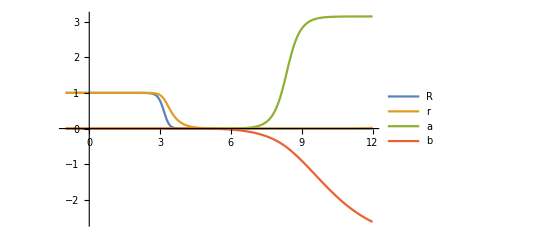

```mathematica
solFuncLeft=Values[solLeft][[1]]
Plot[{solFuncLeft[[1]][z],solFuncLeft[[2]][z],solFuncLeft[[3]][z],solFuncLeft[[4]][z]},{z, zL-1, 12}, PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```

NDSolve::ndsz: At z == -3.14975554024310420918482292295, step size is effectively zero; singularity or stiff system suspected.

{{R→InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],r→InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],a→InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],b→InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>]}}

{InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>],InterpolatingFunction[{{-3.14975554024310420918482292295, 1.00000000000000000000000000000}}, <>]}

InterpolatingFunction::dmval: Input value {-3.9999} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-3.9999} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-3.89786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-3.89786} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-3.79582} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-3.79582} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

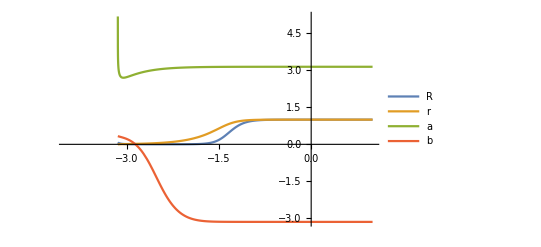

```mathematica
solRight=NDSolve[Join[equations, bcsRight], {R, r, a, b}, {z, -4, zR+1},Method->{"BDF"},WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->10,AccuracyGoal->12]
solFuncRight=Values[solRight][[1]]
Plot[{solFuncRight[[1]][z],solFuncRight[[2]][z],solFuncRight[[3]][z],solFuncRight[[4]][z]},{z,-4,zR+1}, PlotLegends->{"R","r","a","b"}]
```

3.83048

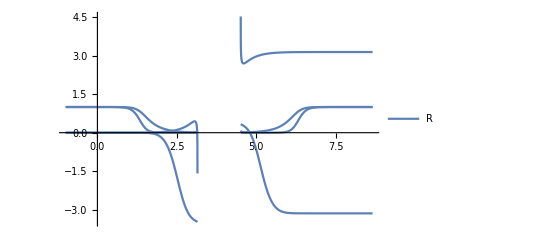

```mathematica
moisei=3.830484591660454
Plot[If[z<moisei, {solFuncLeft[[1]][z],solFuncLeft[[2]][z],solFuncLeft[[3]][z],solFuncLeft[[4]][z]},{solFuncRight[[1]][z-2moisei],solFuncRight[[2]][z-2moisei],solFuncRight[[3]][z-2moisei],solFuncRight[[4]][z-2moisei]}], {z, -1, 2moisei+1},PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```

```mathematica
Minimize[{solFuncLeft[[1]][z], z>0, z<2.47},z]
```

{0.000484958,{z→2.47}}

```mathematica
FindRoot[solFuncLeft[[3]][z]==Pi/2,{z, 1.5}]
```

InterpolatingFunction::dmval: Input value {26.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

{z→3.83048}

```mathematica
FindRoot[solFuncRight[[4]][z]==-Pi/2, {z, -1.5}]
```

InterpolatingFunction::dmval: Input value {-26.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{z→-2.47392}

```mathematica
solFuncLeft[[2]][1.4397038412925143]
```

0.170855

```mathematica
solFuncRight[[2]][-1.4397038412925143]
```

0.170855

```mathematica
D[solFuncLeft[[1]][0]]
```

0.999961635242483807334316512456

```mathematica
N[solFuncLeft[[2]]'[0]]
```

-2.66666

```mathematica
N[8/3 solFuncLeft[[1]][0]-2m solFuncLeft[[2]][0]+solFuncLeft[[3]][0]*N[solFuncLeft[[3]]'[0]]]
```

-0.0000756389

```mathematica
N[8/3 solFuncLeft[[1]][0]Cos[solFuncLeft[[4]][0]]-2m solFuncLeft[[2]][0]Cos[solFuncLeft[[3]][0]]]
```

-0.0000756393

```mathematica
Maximize[{solFuncLeft[[3]][z]+solFuncLeft[[4]][z], z>0, z<2}, z]
```

{0.000617797575451152324940694121153,{z→1.29750086824541081967226416837}}

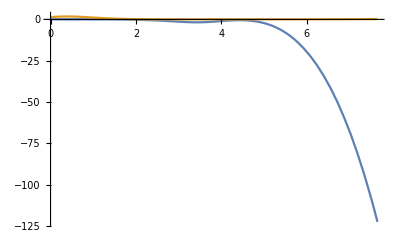

```mathematica
Plot[{solFuncLeft[[3]][z]+solFuncLeft[[4]][z],solFuncRight[[3]][z-moisei]+solFuncRight[[4]][z-moisei]}, {z, 0, 2moisei}, PlotRange->Full]
```

```mathematica
FindRoot[solFuncLeft[[3]][z]+solFuncLeft[[4]][z]==0, {z, 1.4}]
```

{z→1.44678}

```mathematica
FindRoot[solFuncRight[[3]][z]+solFuncRight[[4]][z]==Pi, {z, -3.14}]
```

{z→-3.12181}

```mathematica
FindRoot[solFuncLeft[[3]][z]+solFuncLeft[[4]][z]==-1(solFuncRight[[3]][-z]+solFuncRight[[4]][-z]),{z, 1.5}]
```

{z→1.07722}

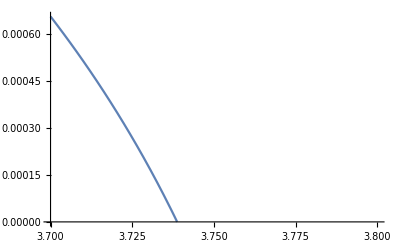

```mathematica
Plot[solFuncLeft[[2]][z],{z, 3.7, 3.8}]
```

```mathematica
solFuncRight[[3]][-3.1218]+solFuncRight[[4]][-3.1218]
```

3.14155

```mathematica
solFuncLeft[[3]][3.1218]+solFuncLeft[[4]][3.1218]
```

-3.14156

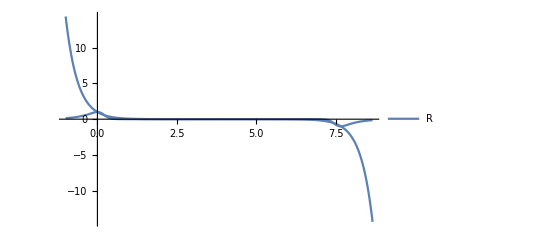

```mathematica
Plot[If[z<moisei, {Re[solFuncLeft[[1]][z]*Exp[I*solFuncLeft[[4]][z]]],Re[solFuncLeft[[2]][z]*Exp[I*solFuncLeft[[3]][z]]]},{Re[solFuncRight[[1]][z-2moisei]*Exp[I*solFuncRight[[4]][z-2moisei]]],Re[solFuncRight[[2]][z-2moisei]*Exp[I*solFuncRight[[3]][z-2moisei]]]}], {z, -1, 2moisei+1},PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```

```mathematica
NSolve[{
0==6 x^(4/3)(Log[y x]Cos[b]-(a+b)Sin[b]),
0==-6 x^(1/3)(Log[y x]Sin[b]+(a+b)Cos[b]),
0==8/3 x Cos[b]-2m y Cos[a],
0==2m Sin[a]-(8x)/(3y)Sin[b]
}/.{x->1, y->1}, {a,b}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ArcCos[Cos[a]]+ArcCos[Cos[b]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{a→-3.14159,b→3.14159},{a→0.,b→0.},{a→3.14159,b→-3.14159}}

```mathematica
FindRoot[solFuncLeft[[3]][z]-Pi/2,{z, 0} ]
```

InterpolatingFunction::dmval: Input value {-15.5468} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.59403} lies outside the range of data in the interpolating function. Extrapolation will be used.

{z→8.36309}

```mathematica
FindRoot[solFuncLeft[[4]][z]+Pi/2, {z, 7}]
```

{z→9.96784}

ParametricFunction[<>]

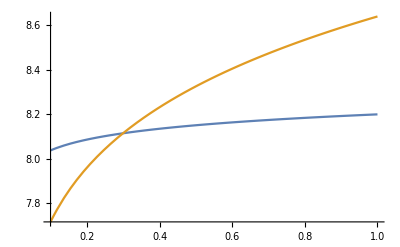

```mathematica
sol=ParametricNDSolveValue[Join[equations, bcsLeft], {R, r, a, b}, {z, zL-1, 10},{s},Method->"ExplicitRungeKutta",WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15]
Plot[{x/.Quiet[FindRoot[sol[s][[3]][x]-Pi/2,{x,0}]],y/.Quiet[FindRoot[sol[s][[4]][y]+Pi/2,{y,0}]]},{s,0.1,1}]
```

```mathematica
Valuessol[0.09]
```

ParametricNDSolveValue::ndsz: At z == 10.7731472529737563619990030242, step size is effectively zero; singularity or stiff system suspected.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
sol[0.2][[3]][2]
```

4.727691564344191332253756068×10^-9

```mathematica
y/.Quiet[FindRoot[sol[0.2][[3]][y]-Pi/2, {y, 0}]]
```

8.08644

```mathematica
alphaPi2[s_]:=Values[Quiet[FindRoot[sol[s][[3]][x]-Pi/2,{x,0}]]]
betaPi2[s_]:=Values[Quiet[FindRoot[sol[s][[4]][x]+Pi/2,{x,0}]]]
```

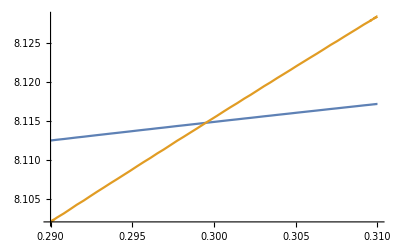

```mathematica
Plot[{alphaPi2[z], betaPi2[z]}, {z, 0.29, 0.31}]
```

```mathematica
Quiet[FindRoot[alphaPi2[x]-betaPi2[x], {x, 0.300}]]
```

{x→0.3}

```mathematica
N[alphaPi2[0.294]-betaPi2[0.294]]
```

{0.00600344}

```mathematica
## Таким образом s=0.294
```

Set::write: Tag Times in Таким образом s ##1 is Protected.

0.294

```mathematica
s=0.294
bcsLeft={
R[zL]==1+eps(-(√313+13)/8)*s,
b[zL]==eps(-√313+13)/8,
r[zL]==1+eps(-1)*s,
a[zL]==eps 
};
bcsRight={
R[zR]==1+eps(-(√313+13)/8)*s,
b[zR]==-Pi+eps(-(-√313+13)/8),
r[zR]==1+eps(-1) *s,
a[zR]==Pi+eps(-1) 
};
```

0.294

NDSolve::precw: The precision of the differential equation ({{R'[z]==6 R[z]^(4/3) (Cos[b[«1»]] Log[Times[«2»]]-(a[«1»]+b[«1»]) Sin[b[«1»]]),b'[z]==-6 R[z]^(1/3) ((a[«1»]+b[«1»]) Cos[b[«1»]]+Log[Times[«2»]] Sin[b[«1»]]),r'[z]==-8/3 Cos[a[z]] r[z]+8/3 Cos[b[z]] R[z],a'[z]==8/3 Sin[a[z]]-(8 R[z] Sin[b[z]])/(3 r[z]),R[0]==1.,b[0]==(13-√313)/8000000000000,r[0]==1.,a[0]==1/1000000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{{R→InterpolatingFunction[…],r→InterpolatingFunction[…],a→InterpolatingFunction[…],b→InterpolatingFunction[…]}}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

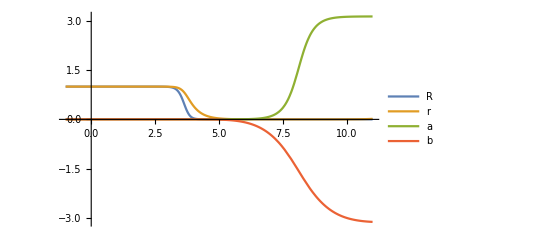

```mathematica
solLeft=NDSolve[Join[equations, bcsLeft], {R, r, a, b}, {z, zL-1, 11},Method->"ExplicitRungeKutta",WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15]
solFuncLeft=Values[solLeft][[1]]
Plot[{solFuncLeft[[1]][z],solFuncLeft[[2]][z],solFuncLeft[[3]][z],solFuncLeft[[4]][z]},{z, zL-1, 11}, PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```

NDSolve::precw: The precision of the differential equation ({{R'[z]==6 R[z]^(4/3) (Cos[b[«1»]] Log[Times[«2»]]-(a[«1»]+b[«1»]) Sin[b[«1»]]),b'[z]==-6 R[z]^(1/3) ((a[«1»]+b[«1»]) Cos[b[«1»]]+Log[Times[«2»]] Sin[b[«1»]]),r'[z]==-8/3 Cos[a[z]] r[z]+8/3 Cos[b[z]] R[z],a'[z]==8/3 Sin[a[z]]-(8 R[z] Sin[b[z]])/(3 r[z]),R[0]==1.,b[0]==(-13+√313)/8000000000000-π,r[0]==1.,a[0]==-1/1000000000000+π},{},{},{},{}}) is less than WorkingPrecision (30.).

{{R→InterpolatingFunction[…],r→InterpolatingFunction[…],a→InterpolatingFunction[…],b→InterpolatingFunction[…]}}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

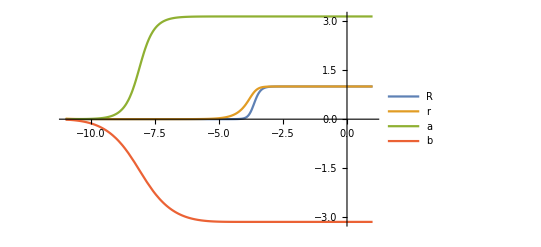

```mathematica
solRight=NDSolve[Join[equations, bcsRight], {R, r, a, b}, {z, -11, zR+1},Method->{"ExplicitRungeKutta"},WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->10,AccuracyGoal->12]
solFuncRight=Values[solRight][[1]]
Plot[{solFuncRight[[1]][z],solFuncRight[[2]][z],solFuncRight[[3]][z],solFuncRight[[4]][z]},{z,-11,zR+1}, PlotLegends->{"R","r","a","b"}]
```

8.11346

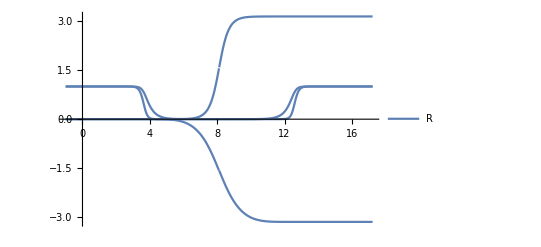

```mathematica
moisei=8.113461017333535
Plot[If[z<moisei, {solFuncLeft[[1]][z],solFuncLeft[[2]][z],solFuncLeft[[3]][z],solFuncLeft[[4]][z]},{solFuncRight[[1]][z-2moisei],solFuncRight[[2]][z-2moisei],solFuncRight[[3]][z-2moisei],solFuncRight[[4]][z-2moisei]}], {z, -1, 2moisei+1},PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```

```mathematica
FindRoot[solFuncRight[[3]][z]-Pi/2,{z, -8}]
```

{z→-8.11346}

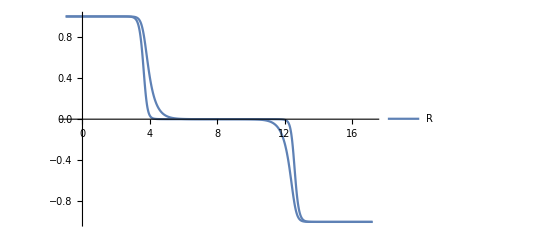

```mathematica
Plot[If[z<moisei, {Re[solFuncLeft[[1]][z]*Exp[I*solFuncLeft[[4]][z]]],Re[solFuncLeft[[2]][z]*Exp[I*solFuncLeft[[3]][z]]]},{Re[solFuncRight[[1]][z-2moisei]*Exp[I*solFuncRight[[4]][z-2moisei]]],Re[solFuncRight[[2]][z-2moisei]*Exp[I*solFuncRight[[3]][z-2moisei]]]}], {z, -1, 2moisei+1},PlotLegends->{"R","r","a","b"}, PlotRange->Full]
```